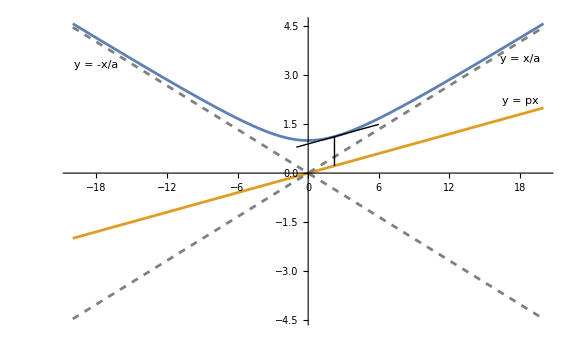

```mathematica
SetDirectory[NotebookDirectory[]];
s =Plot[{√(x^2/20+1),1/10 x,1/(2 √5)x,-1/(2 √5)x},{x,-20,20},PlotStyle->{Automatic, Automatic,{Dashed,Gray}, {Dashed,Gray}},Epilog->{Line[{{√5,(√5)/2},{√5,(√5)/10}}],Line[{{6,1/5 (3+2 √5)},{-1,1/10 (-1+4 √5)}}], Text["y = px", {18,2.2}],Text["y = x/a", {18,3.5}],Text["y = -x/a", {-18,3.3}]},ImageSize->Large,Ticks->None]
```

```mathematica
Export["4_hyperbola.png", s]
```

4_hyperbola.png

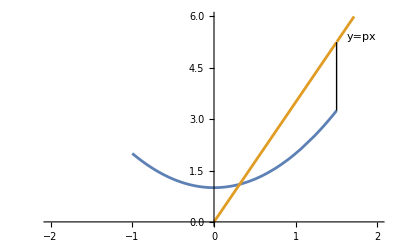

```mathematica
s1=Plot[{Piecewise[{{x^2+1,-1<=x<=1.5}},a],3.5x},{x,-4,4},PlotRange->{{-2,2},{0,6}},Epilog->{Line[{{1.5,1.5^2+1},{1.5,3.5*1.5}}], Text["y=px",{1.8,5.4}]}]
```

```mathematica
Export["4_closed.png", s1]
```

4_closed.png